```mathematica
Clear[Ly,A,
sy2d,SY2D,sy2dp,SY2DP,
cy2d,CY2D,cy2dp,CY2DP,
aMat2d,AMAT2D,CosaMat2d,COSAMAT2D,SinaMat2d,SINAMAT2D,
cons,Cons]
```

```mathematica
Lx=1;
```

```mathematica
Ly = 400;
```

```mathematica
B=1/Ly;
```

```mathematica
A=Lx*Ly;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
aMat2d[i_Integer,j_Integer]=0;

Do[Do[{aMat2d[(k-1) Lx+j,(k-1) Lx+j]=-B*k},{j,1,Lx}],{k,1,Ly}]

AMAT2D=Table[aMat2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
CosaMat2d[i_Integer,j_Integer]=0;

Do[Do[{CosaMat2d[(k-1) Lx+j,(k-1) Lx+j]=Cos[-B*k]},{j,1,Lx}],{k,1,Ly}]

COSAMAT2D=Table[CosaMat2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
SinaMat2d[i_Integer,j_Integer]=0;

Do[Do[{SinaMat2d[(k-1) Lx+j,(k-1) Lx+j]=Sin[-B*k]},{j,1,Lx}],{k,1,Ly}]

SINAMAT2D=Table[SinaMat2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3 ,HamiltonianWSM2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Replace Sin[kx] with Sin[kx-A]=Sin[kx]Cos[A] - Cos[kx]Sin[A]**)
```

```mathematica
(** Replace Cos[kx] with Cos[kx-A]=Cos[kx]Cos[A] + Sin[kx]Sin[A]**)
```

```mathematica
HamiltonianWSM2[t_,m_,kx_,kz_,αy_,tz_]:=2t*(KroneckerProduct[Sin[kx]*COSAMAT2D-Cos[kx]*SINAMAT2D,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+2m * KroneckerProduct[2*Cons-(Cos[kx]*COSAMAT2D+Sin[kx]*SINAMAT2D+CY2D+αy*CY2DP),σ3]+KroneckerProduct[(2 t *Cos[kz])*Cons,σ3]-2 tz * KroneckerProduct[Sin[kx]*COSAMAT2D-Cos[kx]*SINAMAT2D,σ0]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val2,vec2,ValVecAHI2,ValAHI2,ValAHIRange2,β];
β=0.5;
```

```mathematica
(** Weyl point is (kx=0,ky=0,kz=π/2 **)
```

```mathematica
{val2,vec2}=Eigensystem[HamiltonianWSM2[1.,3.,0,(β π)/2,1,0]];
```

```mathematica
ValVecAHI2=SortBy[Transpose[{val2,vec2}],First];
```

```mathematica
ValAHI2=Table[{j,Re[ValVecAHI2[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange2=Table[ValAHI2[[j,2]],{j,1,2 A}];
```

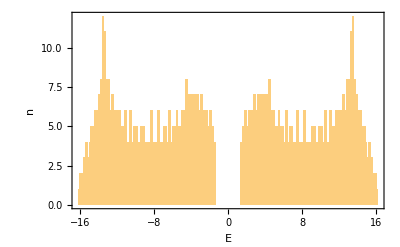

```mathematica
Show[Histogram[val2,100],PlotRange->All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,100]
```

{-3.14159,-3.07876,-3.01593,-2.9531,-2.89027,-2.82743,-2.7646,-2.70177,-2.63894,-2.57611,-2.51327,-2.45044,-2.38761,-2.32478,-2.26195,-2.19911,-2.13628,-2.07345,-2.01062,-1.94779,-1.88496,-1.82212,-1.75929,-1.69646,-1.63363,-1.5708,-1.50796,-1.44513,-1.3823,-1.31947,-1.25664,-1.19381,-1.13097,-1.06814,-1.00531,-0.942478,-0.879646,-0.816814,-0.753982,-0.69115,-0.628319,-0.565487,-0.502655,-0.439823,-0.376991,-0.314159,-0.251327,-0.188496,-0.125664,-0.0628319,0.,0.0628319,0.125664,0.188496,0.251327,0.314159,0.376991,0.439823,0.502655,0.565487,0.628319,0.69115,0.753982,0.816814,0.879646,0.942478,1.00531,1.06814,1.13097,1.19381,1.25664,1.31947,1.3823,1.44513,1.50796,1.5708,1.63363,1.69646,1.75929,1.82212,1.88496,1.94779,2.01062,2.07345,2.13628,2.19911,2.26195,2.32478,2.38761,2.45044,2.51327,2.57611,2.63894,2.70177,2.7646,2.82743,2.89027,2.9531,3.01593,3.07876,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

101

```mathematica
(** tz = 0.5 **)
```

```mathematica
Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,0,kzVector[[i]],1,0.5]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]
```

```mathematica
Clear[listplotOfenergyWithKz,listplotOfenergyWithKz2]
```

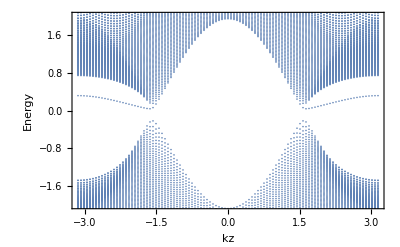

```mathematica
listplotOfenergyWithKz=Show[ListPlot[b,PlotRange->{All,{-2,2}} ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

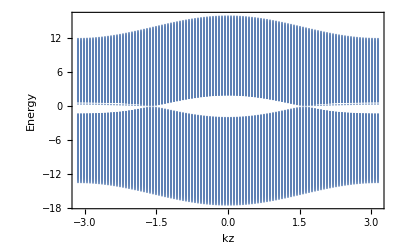

```mathematica
listplotOfenergyWithKz2=Show[ListPlot[b,PlotRange->All ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

```mathematica
(** t0x = 0 **)
```

```mathematica
Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,0,kzVector[[i]],1,0]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]
```

```mathematica
Clear[listplotOfenergyWithKz3,listplotOfenergyWithKz4]
```

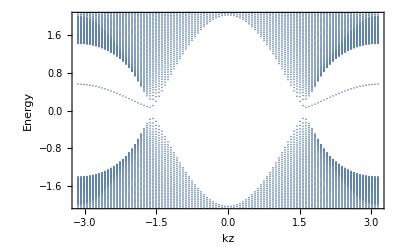

```mathematica
listplotOfenergyWithKz3=Show[ListPlot[bb,PlotRange->{All,{-2,2}} ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

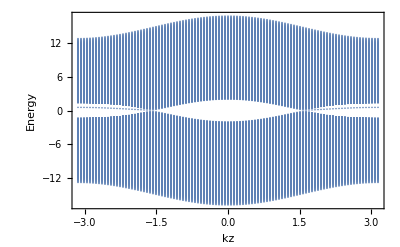

```mathematica
listplotOfenergyWithKz4=Show[ListPlot[bb,PlotRange->All ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

```mathematica
(** tz = 1 **)
```

```mathematica
Clear[bbb];
bbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,0,kzVector[[i]],1,1]],
Do[bbb=Append[bbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]
```

```mathematica
Clear[listplotOfenergyWithKz5,listplotOfenergyWithKz6]
```

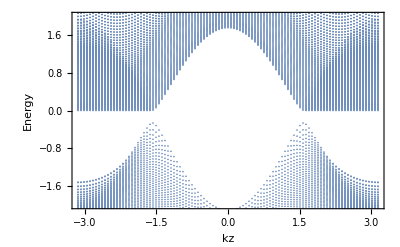

```mathematica
listplotOfenergyWithKz5=Show[ListPlot[bbb,PlotRange->{All,{-2,2}} ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

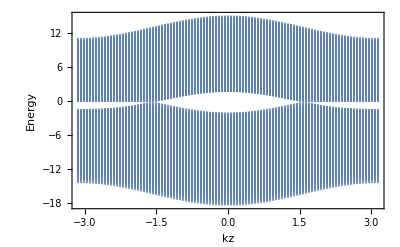

```mathematica
listplotOfenergyWithKz6=Show[ListPlot[bbb,PlotRange->All ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

```mathematica
(** tz = 1.5 **)
```

```mathematica
Clear[bbbb];
bbbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,0,kzVector[[i]],1,1.5]],
Do[bbbb=Append[bbbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]
```

```mathematica
Clear[listplotOfenergyWithKz7, listplotOfenergyWithKz8]
```

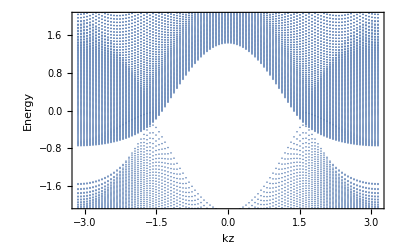

```mathematica
listplotOfenergyWithKz7=Show[ListPlot[bbbb,PlotRange->{All,{-2,2}} ],AxesLabel-> {"kz","Energy"},Frame-> True]
```

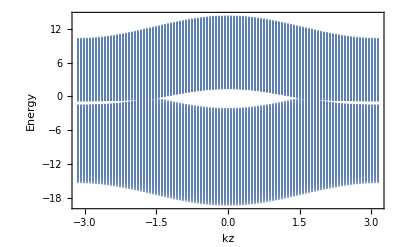

```mathematica
listplotOfenergyWithKz8=Show[ListPlot[bbbb,PlotRange->All ],AxesLabel-> {"kz","Energy"},Frame-> True]
```